```mathematica
data={1,2,3,4,5,6,7,8,9,10};
```

```mathematica
StandardDeviation[data]//N
StandardDeviation[data^2]//N
```

3.02765

34.1736

```mathematica
4 π n^2∫_0^∞ ⅇ^(-2r/a)rⅆr 
∫_0^∞ ⅇ^(-2r/a)r^2ⅆr
```

4 n^2 π If[Re[a]>0,a^2/4,Integrate[ⅇ^(-(2 r)/a) r,{r,0,∞},Assumptions→Re[a]≤0]]

If[Re[a]>0,a^3/4,Integrate[ⅇ^(-(2 r)/a) r^2,{r,0,∞},Assumptions→Re[a]≤0]]

```mathematica
D[(D[(x D[ⅇ^(a x), x]), x]), x]-x D[D[D[ⅇ^(a x), x], x], x]
```

2 a^2 ⅇ^(a x)

```mathematica
2 D[D[ⅇ^x, x], x]
```

2 ⅇ^x

```mathematica
∫ArcCos[2x/l]ⅆx
```

-1/2 l √(1-(4 x^2)/l^2)+x ArcCos[(2 x)/l]

```mathematica
ArcCos[-0.5]-π
```

-1.0472

```mathematica
2∫_0^(l/2) ArcCos[x/(l/2)]ⅆx
```

l

```mathematica
daaa={1,2,3,4,5,6,7,8,9,10};
d1={2.50,5,3.333,3.333,3.333,5,2,2.5,2,2};
d2={3.333,3.125,3.106, 3.187};
dd1=Table[{daaa[[i]],d1[[i]]},{i,1,10}];
```

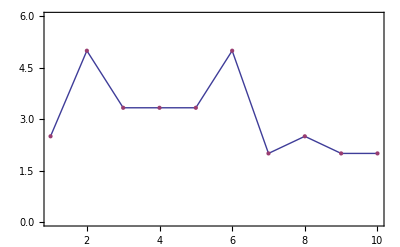

```mathematica
ListPlot[{d,d},Joined->{True,False},PlotRange->{0,6},Frame->True]
```

```mathematica
dd2=Table[{daaa[[i]],d1[[i]]},{i,1,4}];
dd3={{10,3.333},{20,3.333},{30,3.75},{40,3.077},{50,3.333},{60,3.333},{70,3.043},{80,2.857},{90,2.812},{100,2.857},{200,2.703},{400,3.2},{600,3.209},{800,3.226},{1000,3.155},{2000,3.185},{4000,3.185},{6000,3.151},{8000,3.168},{10000,3.131},{20000,3.153},{30000,3.13},{40000,3.139},{50000,3.13}};
```

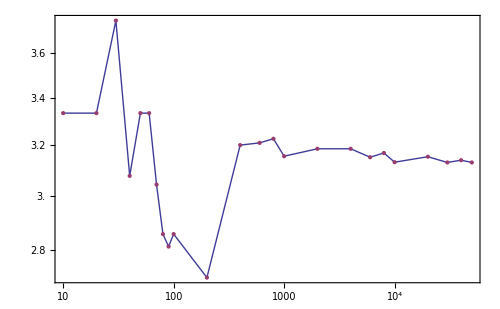

```mathematica
ListLogLogPlot[{dd3,dd3},Joined->{True,False},Frame->True]
```